```mathematica
Get["/home/saul/Documents/Wolfram/MatrixComponent.wl"]
```

```mathematica
MatCoordinate[dim_]:=Flatten[Table[{i,j},{i,dim},{j,dim}],1]
RandomEntryGenerator[dim_]:=RandomVariate[NormalDistribution[0,1],dim^2]
RandomMatrix[dim_]:=CreateArray[MatCoordinate[dim],RandomEntryGenerator[dim]]
SymmetricRandomMatrix[dim_]:=Module[{R=RandomMatrix[dim]},R+Transpose[R]]

(*Primera entrada la dimension deseada para las matrices, segunda entrada el numero de matrices a usar*)
SymmetricRandomMatrixMatrixListGenerator[dim_,N_]:=Table[SymmetricRandomMatrix[dim],{i,N}]

(*Una lista de todos los eigenvalores que retorna los MatrixListGenerator*)
TotalEigenValues[ArrayList_]:=Table[Last /@ EigenInfo[ArrayList[[i]]],{i,Length[ArrayList]}]//Flatten

CreateHistogram[list_]:=Histogram[list,{Min[list],Max[list],(2*InterquartileRange[list])/(n^(1/3))},"PDF"]

(*Distancia entre eigenvalores adyacentes segun un orden dado*)
KLevelSpacing[list_,order_]:=Module[{k=order,Sortedlist=Sort[list],n=Length[list]},
Table[Sortedlist[[i+k]]-Sortedlist[[i]],{i,1,n-k}]]
```

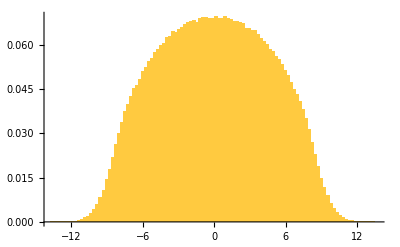

```mathematica
dim=10;
n=200000;
S=SymmetricRandomMatrixMatrixListGenerator[dim,n];
T=TotalEigenValues[S];
CreateHistogram[T]
```

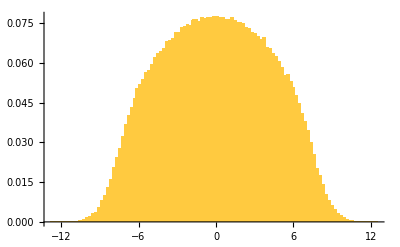

```mathematica
dim1=8;
n1=100000;
S1=SymmetricRandomMatrixMatrixListGenerator[dim1,n1];
E1=Last /@ EigenInfo[S1[[1]]];
KLevelSpacing[E1,1];
SpacingVals=Table[Last /@ EigenInfo[S1[[i]]],{i,Length[S1]}]//Flatten;
CreateHistogram[SpacingVals]
```

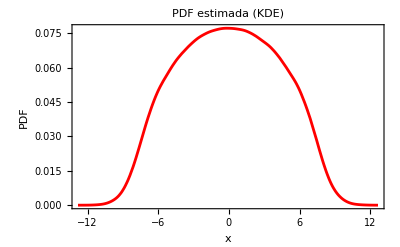

```mathematica
dist=SmoothKernelDistribution[SpacingVals];

Plot[PDF[dist,x],{x,Min[SpacingVals],Max[SpacingVals]},PlotRange->All,PlotStyle->Red,PlotLabel->"PDF estimada (KDE)",AxesLabel->{"x","PDF"},Frame->True]
```